## Higgs decays in the Standard Model

## Initialization cells

#### Setup

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts = True;
<<FeynCalc`;
$FAVerbose=0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Global`$FeynCalcStartupMessages::shdw: Symbol $FeynCalcStartupMessages appears in multiple contexts {Global`,FeynCalc`}; definitions in context Global` may shadow or be shadowed by other definitions.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, in preparation

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

#### Settings

```mathematica
$BreitMaison=True;
$Larin=False;
(*$West=False;*)
$Assumptions={MH>0,MQD[Index[Generation,4]]>0,MQU[Index[Generation,4]]>0,MLE[Index[Generation,4]]>0,SMP["m_H"]>0,SMP["m_W"]>0,SMP["m_b"]>0, SMP["m_t"]> 0,SMP["m_tau"]>0,SMP["m_W"]>0};
```

#### Definitions

```mathematica
LandauGauge={GaugeXi->0};
FeynmanGauge={GaugeXi-> 1};
YennieGauge={GaugeXi->3};
preFactor=-ⅈ/(2 π)^D; (*Prefactor that comes with the momentum integration*)
replaceFac1={MQD[_,_]:> SMP["m_b"],MQU[_,_]:> SMP["m_t"],MLE[_]:> SMP["m_e"],yd[_,_]:> Sqrt[2]SMP["e"]SMP["m_b"]/(2SMP["m_W"]SMP["sin_W"]),yu[_,_]:> Sqrt[2]SMP["e"]SMP["m_t"]/(2SMP["m_W"]SMP["sin_W"]),yl[_,_]:>Sqrt[2] SMP["e"]SMP["m_e"]/(2SMP["m_W"]SMP["sin_W"]),MW:> SMP["m_W"],MZ:> SMP["m_Z"],EL:> SMP["e"],sw:> SMP["sin_W"],cw:> SMP["cos_W"],g1z:> SMP["g_Z"],sz:> SMP["sin_Z"],cz:> SMP["cos_Z"],sg->  SMP["sin_G"],cg->  SMP["cos_G"],sa->  SMP["sin_H"],ca->  SMP["cos_H"],lam1-> (SMP["cos_H"]^2SMP["m_H"]^2+SMP["sin_H"]^2MH2^2)/2/vev^2,lam3->SMP["cos_H"]SMP["sin_H"] (MH2^2-SMP["m_H"]^2)/(Sqrt[RR*vev^2]vev)};
replaceFac2={vev-> 2SMP["m_W"]SMP["sin_W"]/SMP["e"]};
smLimit={SMP["sin_Z"]:> 0,SMP["cos_Z"]:> 1,SMP["sin_G"]:> 0,SMP["cos_G"]:> 1,SMP["g_Z"]:> 0,SMP["sin_H"]:> 0,SMP["cos_H"]:> 1};
```

```mathematica
(*The replacements above are just for presentation. The file SMP.m (attached) can be put in the ~/../Applications/FeynCalc/Feynma folder. You can also add your own graphics in the SMP.m file*)
```

#### Setup

```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
		Print["Computation of the 1-loop gluon self-energy in QCD"];
];
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts = True;
<<FeynCalc`;
$FAVerbose=0;
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

#### Settings

```mathematica
$BreitMaison=True;
$Larin=False;
(*$West=False;*)
$Assumptions={MH>0,MQD[Index[Generation,4]]>0,MQU[Index[Generation,4]]>0,MLE[Index[Generation,4]]>0,SMP["m_H"]>0,SMP["m_W"]>0,SMP["m_b"]>0, SMP["m_t"]> 0,SMP["m_tau"]>0,SMP["m_W"]>0};
```

#### Definitions

```mathematica
LandauGauge={GaugeXi->0};
FeynmanGauge={GaugeXi-> 1};
YennieGauge={GaugeXi->3};
preFactor=-ⅈ/(2 π)^D;
replaceFac1={MQD[_,_]:> SMP["m_b"],MQU[_,_]:> SMP["m_t"],MLE[_]:> SMP["m_e"],yd[_,_]:> Sqrt[2]SMP["e"]SMP["m_b"]/(2SMP["m_W"]SMP["sin_W"]),yu[_,_]:> Sqrt[2]SMP["e"]SMP["m_t"]/(2SMP["m_W"]SMP["sin_W"]),yl[_,_]:>Sqrt[2] SMP["e"]SMP["m_e"]/(2SMP["m_W"]SMP["sin_W"]),MW:> SMP["m_W"],MZ:> SMP["m_Z"],EL:> SMP["e"],sw:> SMP["sin_W"],cw:> SMP["cos_W"],g1z:> SMP["g_Z"],sz:> SMP["sin_Z"],cz:> SMP["cos_Z"],sg->  SMP["sin_G"],cg->  SMP["cos_G"],sa->  SMP["sin_H"],ca->  SMP["cos_H"],lam1-> (SMP["cos_H"]^2SMP["m_H"]^2+SMP["sin_H"]^2MH2^2)/2/vev^2,lam3->SMP["cos_H"]SMP["sin_H"] (MH2^2-SMP["m_H"]^2)/(Sqrt[RR*vev^2]vev),ZH-> SMP["z_H"]};
replaceFac2={Zu-> Zq+SMP["z_H"],Zd-> Zq-SMP["z_H"],Ze-> Zl-SMP["z_H"],vev-> 2SMP["m_W"]SMP["sin_W"]/SMP["e"],SMP["cos_G"]:> SMP["m_W"](SMP["cos_Z"]SMP["e"]-SMP["z_H"]SMP["g_Z"]SMP["sin_Z"]SMP["sin_W"]SMP["cos_W"])/(SMP["cos_W"]SMP["e"]SMP["m_Z"]),SMP["sin_G"]:> SMP["m_W"](SMP["sin_Z"]SMP["e"]+SMP["z_H"]SMP["g_Z"]SMP["cos_Z"]SMP["sin_W"]SMP["cos_W"])/(SMP["cos_W"]SMP["e"]SMP["m_Zp"]),(SMP["cos_W"])^2-> 1-(SMP["sin_W"])^2};

replaceFacNoMix={SMP["cos_Z"]:> 1,SMP["sin_Z"]:> 0,SMP["cos_G"]:> 1,SMP["sin_G"]:> 0,SMP["z_H"]:> 0 };smLimit={SMP["sin_Z"]:> 0,SMP["cos_Z"]:> 1,SMP["sin_G"]:> 0,SMP["cos_G"]:> 1,SMP["g_Z"]:> 0,SMP["sin_H"]:> 0,SMP["cos_H"]:> 1};
replaceFacAnomaly={Ey:> -3/2(Zl+3Zq),K2:> -3(Zl+3Zq),Ez:> -3/4 SMP["z_H"](Zl+3Zq),Cz:> -9/(4MI) SMP["z_H"](Zl+3Zq),D2:>3/(MI)(Zl+3Zq),Cy:> -3/(2MI)(Zl+3Zq),Cx:> -3a/(2MI)(-SMP["z_H"]^3-3 SMP["z_H"] Zl^2-Zl^3+3SMP["z_H"]^2(Zl+6Zq))}; 
replaceFacMassless={SMP["m_b"]:> 0,SMP["m_t"]:> 0,SMP["m_e"]:> 0};
```

```mathematica
replaceFacAmp={Log[(2SMP["m_b"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_b"]^2SMP["m_Z"]^2])/(2SMP["m_b"]^2)]:> AbZ,Log[(2SMP["m_b"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_b"]^2SMP["m_Zp"]^2])/(2SMP["m_b"]^2)]:> AbZp,Log[(2SMP["m_t"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_t"]^2SMP["m_Z"]^2])/(2SMP["m_t"]^2)]:> AtZ,Log[(2SMP["m_t"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_t"]^2SMP["m_Zp"]^2])/(2SMP["m_t"]^2)]:> AtZp,Log[(2SMP["m_e"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_e"]^2SMP["m_Z"]^2])/(2SMP["m_e"]^2)]:> AeZ,Log[(2SMP["m_e"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_e"]^2SMP["m_Zp"]^2])/(2SMP["m_e"]^2)]:> AeZp};
```

```mathematica
log[x_ y_]:= log[x]+log[y]
log[x_ /y_]:= log[x]-log[y]
log[x_ ^y_]:=y log[x]
```

## q1 q2>q1 q2

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

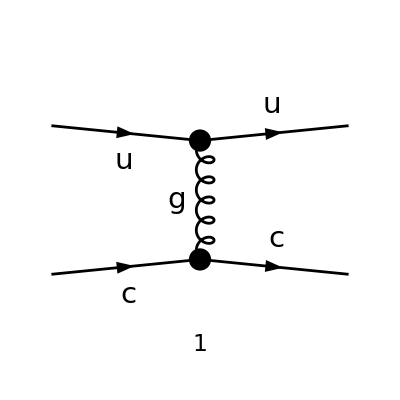

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&
```

-(g_s^2 T_Col3Col1^Glu5 T_Col4Col2^Glu5 (φ(OverBar[k2],m_c)).(γ̄)^Lor2.(φ(OverBar[p2],m_c)) (φ(OverBar[k1],m_u)).(γ̄)^Lor2.(φ(OverBar[p1],m_u)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[amp[0]*ComplexConjugate[amp[0]]]]]]//SUNSimplify[#,Explicit->True]&
```

(C_A C_F g_s^4 (2 m_c^2 (-2 m_e^2+4 m_u^2+t)-2 m_e^2 (-2 m_μ^2+s+u)+2 m_e^4+2 m_μ^4-2 s m_μ^2+2 t m_u^2-2 u m_μ^2-4 m_μ^2 m_u^2+s^2+u^2))/t^2

```mathematica
ampSquaredMassless1[0]=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0}&)[ampSquared[0]]]//Simplify
```

(C_A C_F g_s^4 (s^2+u^2))/t^2

## q1 q2b>q1 q2b

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

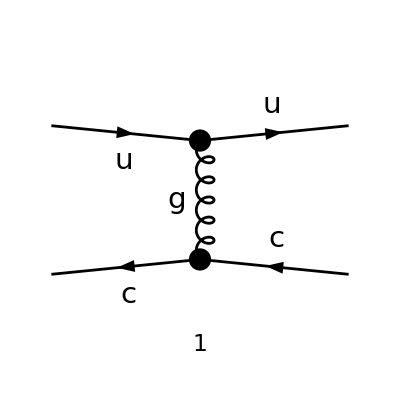

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{1}],-F[3,{2}]}->{F[3,{1}],-F[3,{2}]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&
```

(g_s^2 T_Col3Col1^Glu5 T_Col2Col4^Glu5 (φ(-OverBar[p2],m_c)).(γ̄)^Lor2.(φ(-OverBar[k2],m_c)) (φ(OverBar[k1],m_u)).(γ̄)^Lor2.(φ(OverBar[p1],m_u)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[amp[0]*ComplexConjugate[amp[0]]]]]]//SUNSimplify[#,Explicit->True]&
```

(C_A C_F g_s^4 (2 m_c^2 (-2 m_e^2+4 m_u^2+t)-2 m_e^2 (-2 m_μ^2+s+u)+2 m_e^4+2 m_μ^4-2 s m_μ^2+2 t m_u^2-2 u m_μ^2-4 m_μ^2 m_u^2+s^2+u^2))/t^2

```mathematica
ampSquaredMassless1[0]=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0}&)[ampSquared[0]]]//Simplify
```

(C_A C_F g_s^4 (s^2+u^2))/t^2

## q1 q1b>q2 q2b

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

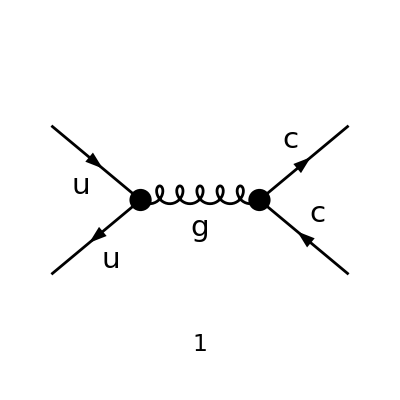

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{1}],-F[3,{1}]}->{F[3,{2}],-F[3,{2}]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&
```

-(g_s^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(OverBar[k1],m_c)).(γ̄)^Lor1.(φ(-OverBar[k2],m_c)) (φ(-OverBar[p2],m_u)).(γ̄)^Lor1.(φ(OverBar[p1],m_u)))/(OverBar[k1]+OverBar[k2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1]&)[FeynAmpDenominatorExplicit[amp*ComplexConjugate[amp]]]]]//SUNSimplify[#,Explicit->True]&
```

(4 C_A C_F g_s^4 (2 m_c^2 (-m_e^2-m_μ^2+4 m_u^2+s)-2 m_e^2 (-3 m_μ^2+m_u^2+t+u)+m_e^4+m_μ^4+2 s m_u^2-2 t m_μ^2-2 u m_μ^2-2 m_μ^2 m_u^2+t^2+u^2))/s^2

```mathematica
ampSquaredMassless1=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0}&)[ampSquared[0]]]//Simplify
```

(4 C_A C_F g_s^4 (t^2+u^2))/s^2

```mathematica
ampSquaredMassless1/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(4 C_A C_F g_s^4 (t^2+u^2))/s^2/.RepComp

```mathematica
Litt=8 dF^2*CF^2/dA(t^2+u^2)/s^2/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(8 dF^2 C_F^2 (t^2+u^2))/(dA s^2)/.RepComp

## q1 q1b>gg - diff

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

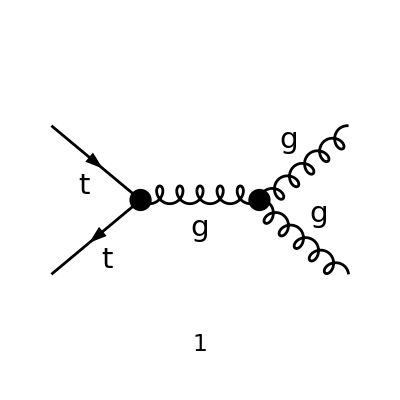

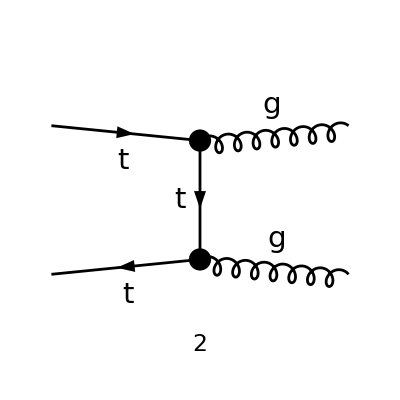

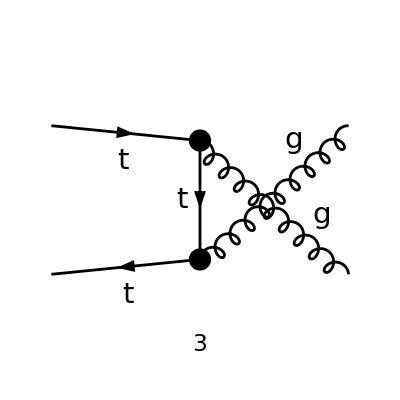

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],-F[3,{3}]}->{V[5],V[5]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,SMP->True,Contract->True(**),DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&;
```

```mathematica
amp[[1]]
```

1/(OverBar[k1]+OverBar[k2])^2 2 g_s^2 T_Col2Col1^Glu5 (tr(T^Glu3.T^Glu4.T^Glu5)-tr(T^Glu4.T^Glu3.T^Glu5)) ((OverBar[k1]·(ε̄)^*(k1)) (φ(-OverBar[p2],m_t)).(γ̄·(ε̄)^*(k2)).(φ(OverBar[p1],m_t))-2 (OverBar[k1]·(ε̄)^*(k2)) (φ(-OverBar[p2],m_t)).(γ̄·(ε̄)^*(k1)).(φ(OverBar[p1],m_t))+2 (OverBar[k2]·(ε̄)^*(k1)) (φ(-OverBar[p2],m_t)).(γ̄·(ε̄)^*(k2)).(φ(OverBar[p1],m_t))-(OverBar[k2]·(ε̄)^*(k2)) (φ(-OverBar[p2],m_t)).(γ̄·(ε̄)^*(k1)).(φ(OverBar[p1],m_t))+((ε̄)^*(k1)·(ε̄)^*(k2)) (φ(-OverBar[p2],m_t)).(γ̄·(OverBar[k1]-OverBar[k2])).(φ(OverBar[p1],m_t)))

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,0,0];
```

```mathematica
amp2=Sum[i,{i,amp}];
```

```mathematica
amp3=FeynAmpDenominatorExplicit[amp2*ComplexConjugate[amp2]]//SUNSimplify[#,Explicit->True]&;
```

```mathematica
amp4=amp3//DoPolarizationSums[#,k1,0]&//DoPolarizationSums[#,k2,0]&;
```

```mathematica
amp5=Simplify[DiracSimplify[(FermionSpinSum[amp4])]];
```

```mathematica
ampSquaredMassless1=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0,SMP["m_t"]->0}&)[amp5]]//Simplify
```

(g_s^4 (8 s^2 C_A C_F^2 (t^2+u^2)+C_A (C_A^2-1) (2 s^3 (t+u)+s^2 (4 t^2+3 t u+4 u^2)+2 s (t-u)^2 (t+u)-t u (7 t^2+4 t u+7 u^2))+8 s^3 C_F (s+t+u)))/(s^2 t u)

```mathematica
TrickMandelstam[#,{s,t,u,0}]&/@ampSquaredMassless1/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 C_A g_s^4 (-2 t^3 u C_A^2+t^2 u^2 C_A^2-2 t u^3 C_A^2+4 s^2 t^2 C_F^2+4 s^2 u^2 C_F^2+2 t^3 u-t^2 u^2+2 t u^3))/(s^2 t u)/.RepComp

```mathematica
Litt=8dF*CF^2(u/t+t/u)-8 dF CF CA((t^2+u^2)/s^2)/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8 dF C_F^2 (t/u+u/t)-(8 dF C_A C_F (t^2+u^2))/s^2/.RepComp

## q1 g>q1 g

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

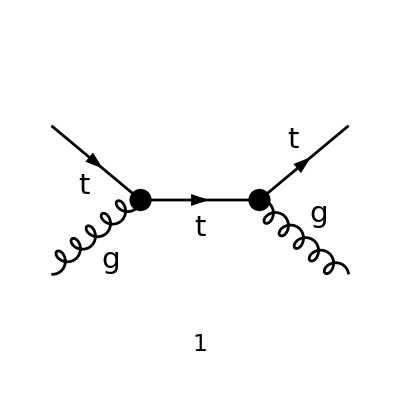

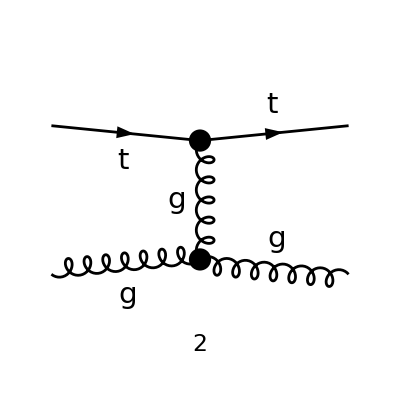

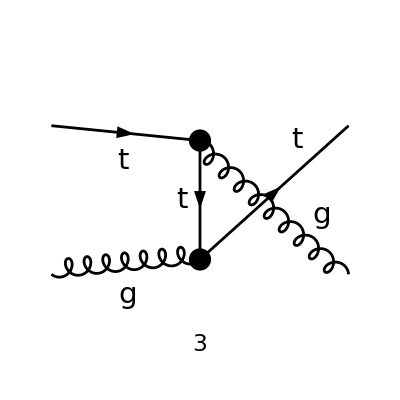

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],V[5]}->{F[3,{3}],V[5]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,SMP->True,Contract->True(**),DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,0,0];
```

```mathematica
amp2=Sum[i,{i,amp}]
```

-(g_s^2 (T^Glu2 T^Glu4)_Col3Col1 (φ(OverBar[k1],m_t)).(γ̄·ε̄(p2)).(γ̄·(OverBar[k1]-OverBar[p2])+m_t).(γ̄·(ε̄)^*(k2)).(φ(OverBar[p1],m_t)))/((OverBar[p2]-OverBar[k1])^2-m_t^2)-(g_s^2 (T^Glu4 T^Glu2)_Col3Col1 (φ(OverBar[k1],m_t)).(γ̄·(ε̄)^*(k2)).(γ̄·(OverBar[k1]+OverBar[k2])+m_t).(γ̄·ε̄(p2)).(φ(OverBar[p1],m_t)))/((-OverBar[k1]-OverBar[k2])^2-m_t^2)-1/(OverBar[k2]-OverBar[p2])^2 2 g_s^2 T_Col3Col1^Glu5 (tr(T^Glu2.T^Glu4.T^Glu5)-tr(T^Glu4.T^Glu2.T^Glu5)) ((OverBar[k2]·(ε̄)^*(k2)) (φ(OverBar[k1],m_t)).(γ̄·ε̄(p2)).(φ(OverBar[p1],m_t))-2 (OverBar[k2]·ε̄(p2)) (φ(OverBar[k1],m_t)).(γ̄·(ε̄)^*(k2)).(φ(OverBar[p1],m_t))-2 (OverBar[p2]·(ε̄)^*(k2)) (φ(OverBar[k1],m_t)).(γ̄·ε̄(p2)).(φ(OverBar[p1],m_t))+(OverBar[p2]·ε̄(p2)) (φ(OverBar[k1],m_t)).(γ̄·(ε̄)^*(k2)).(φ(OverBar[p1],m_t))+((ε̄)^*(k2)·ε̄(p2)) (φ(OverBar[k1],m_t)).(γ̄·(OverBar[k2]+OverBar[p2])).(φ(OverBar[p1],m_t)))

```mathematica
amp3=FeynAmpDenominatorExplicit[amp2*ComplexConjugate[amp2]]//SUNSimplify[#,Explicit->True]&;
```

```mathematica
amp4=amp3//DoPolarizationSums[#,p2,0]&//DoPolarizationSums[#,k2,0]&;
```

```mathematica
amp5=Simplify[DiracSimplify[(FermionSpinSum[amp4])]];
```

```mathematica
ampSquaredMassless1=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0,SMP["m_t"]->0}&)[amp5]]//Simplify
```

-1/(s t^2 u)g_s^4 (C_A (2 s^2 (t^2 (4 C_F^2-2)+t u+2 u^2)-2 t u (t u (2-4 C_F^2)+t^2+u^2)+s^3 (7 u-2 t)+s (-2 t^3-3 t^2 u+2 t u^2+7 u^3))+C_A^3 (s^3 (2 t-7 u)+s^2 (4 t^2-2 t u-4 u^2)+s (2 t^3+3 t^2 u-2 t u^2-7 u^3)+2 t u (t+u)^2)+8 t^3 C_F (s+t+u))

```mathematica
Res=TrickMandelstam[#,{s,t,u,0}]&/@ampSquaredMassless1//Expand
```

-(8 u C_A C_F^2 g_s^4)/s-(8 s C_A C_F^2 g_s^4)/u+(10 u^2 C_A^3 g_s^4)/t^2-(10 u^2 C_A g_s^4)/t^2+(10 u C_A^3 g_s^4)/t-(10 u C_A g_s^4)/t+4 C_A^3 g_s^4-4 C_A g_s^4

```mathematica
Litt=-8 dF CF^2(u/s+s/u)+8 dF CF CA ((s^2+u^2)/t^2)//Expand
```

(8 dF s^2 C_A C_F)/t^2+(8 dF u^2 C_A C_F)/t^2-(8 dF u C_F^2)/s-(8 dF s C_F^2)/u

```mathematica
Res/.u->-s-t//Series[#,{t,0,2}]&
```

(10 s^2 C_A^3 g_s^4-10 s^2 C_A g_s^4)/t^2+(10 s C_A^3 g_s^4-10 s C_A g_s^4)/t+(16 C_A C_F^2 g_s^4+4 C_A^3 g_s^4-4 C_A g_s^4)+(8 t^2 C_A C_F^2 g_s^4)/s^2+O(t^3)

```mathematica
Litt/.u->-s-t//Series[#,{t,0,2}]&
```

(16 dF s^2 C_A C_F)/t^2+(16 dF s C_A C_F)/t+(8 dF C_A C_F+16 dF C_F^2)+(8 dF t^2 C_F^2)/s^2+O(t^3)

```mathematica
240 u^2-240( s+u)u+96 (s+u)^2//Expand
```

96 s^2-48 s u+96 u^2

## g g>g g New-Works

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

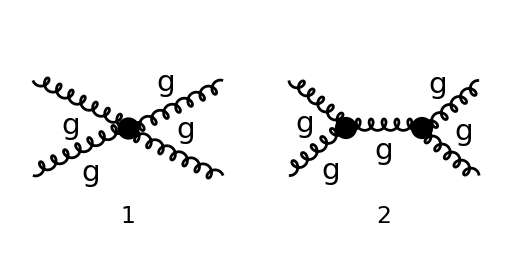

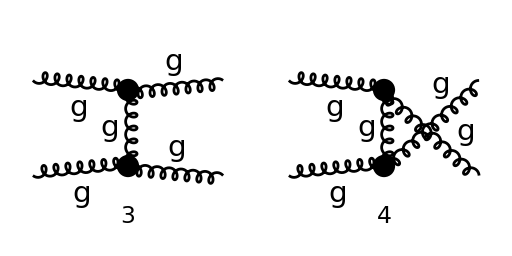

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{V[5],V[5]}->{V[5],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(1/(SUNN^2-1)^2)*(amp[1]*ComplexConjugate[amp[0]])]];
```

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[amp[0][[i]]*ComplexConjugate[amp[0]][[j]]]]][[1]]];
re[i,j],{i,4},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.201862

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.232933

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.116161

calculating color factors in products of the    amplitudes 3 and 1 (CC), time = 0.232705

calculating color factors in products of the    amplitudes 3 and 2 (CC), time = 0.124323

calculating color factors in products of the    amplitudes 3 and 3 (CC), time = 0.117425

calculating color factors in products of the    amplitudes 4 and 1 (CC), time = 0.233223

calculating color factors in products of the    amplitudes 4 and 2 (CC), time = 0.125608

calculating color factors in products of the    amplitudes 4 and 3 (CC), time = 0.12504

calculating color factors in products of the    amplitudes 4 and 4 (CC), time = 0.11905

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[(polsums[#1,k2,k1,1]&)[(polsums[#1,k1,k2,1]&)[re[i,j]]]]]]][[1]]];
pre[i,j],{i,4},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.247554

calculating product of the amplitudes 2 and 1 (CC), time = 0.302165

calculating product of the amplitudes 2 and 2 (CC), time = 0.997334

calculating product of the amplitudes 3 and 1 (CC), time = 0.466626

calculating product of the amplitudes 3 and 2 (CC), time = 1.29396

calculating product of the amplitudes 3 and 3 (CC), time = 1.36776

calculating product of the amplitudes 4 and 1 (CC), time = 0.502295

calculating product of the amplitudes 4 and 2 (CC), time = 1.3359

calculating product of the amplitudes 4 and 3 (CC), time = 1.59462

calculating product of the amplitudes 4 and 4 (CC), time = 1.38143

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,4},{j,1,4}]]]
```

(16 N^2 (N^2-1) g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)

```mathematica
ampSquaredSUNN3[0]=ampSquared[0]/. SUNN->3
```

(1152 g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)

```mathematica
ampSquaredMassless[0]=(TrickMandelstam[#1,{s,t,u,0}]&)[(#1/. {SMP["m_u"]->0}&)[ampSquared[0]]]
```

-(16 N^2 (1-N^2) g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)

```mathematica
ampSquaredMasslessSUNN3[0]=ampSquaredMassless[0]/. SUNN->3
```

(1152 g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)

```mathematica
Res=ampSquaredMasslessSUNN3[0]/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(1152 g_s^4 (t^2+t u+u^2)^3)/(s^2 t^2 u^2)/.RepComp

```mathematica
Litt=16 dA CA^2(3- s u /t^2-s t /u^2- t u /s^2)/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

16 dA C_A^2 (-(t u)/s^2-(s u)/t^2-(s t)/u^2+3)/.RepComp

## q1 q1b>gg - New Works

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],-F[3,{3}]}->{V[5],V[5]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp[1]*ComplexConjugate[amp[0]])]];
```

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[amp[0][[i]]*ComplexConjugate[amp[0]][[j]]]]][[1]]];
re[i,j],{i,amp[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.080843

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.071243

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.049478

calculating color factors in products of the    amplitudes 3 and 1 (CC), time = 0.07374

calculating color factors in products of the    amplitudes 3 and 2 (CC), time = 0.050006

calculating color factors in products of the    amplitudes 3 and 3 (CC), time = 0.047481

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]]//ReplaceAll[#,SMP["m_t"]->0]&;//Simplify]];
re2[i,j],{i,amp[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.239206,Null}

Doing spin sums2 and 1 (CC), time = {0.185346,Null}

Doing spin sums2 and 2 (CC), time = {0.181055,Null}

Doing spin sums3 and 1 (CC), time = {0.189696,Null}

Doing spin sums3 and 2 (CC), time = {0.296708,Null}

Doing spin sums3 and 3 (CC), time = {0.180862,Null}

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.151217

calculating product of the amplitudes 2 and 1 (CC), time = 0.171176

calculating product of the amplitudes 2 and 2 (CC), time = 0.144597

calculating product of the amplitudes 3 and 1 (CC), time = 0.147235

calculating product of the amplitudes 3 and 2 (CC), time = 0.197482

calculating product of the amplitudes 3 and 3 (CC), time = 0.116411

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp[0]//Length},{j,1,amp[0]//Length}]]]
```

(2 (N^2-1) g_s^4 (t^2+u^2) (N^2 (t^2+u^2)-s^2))/(N s^2 t u)

```mathematica
ampSquaredSUNN3[0]=ampSquared[0]/. SUNN->3
```

(16 g_s^4 (t^2+u^2) (9 (t^2+u^2)-s^2))/(3 s^2 t u)

```mathematica
Res=ampSquaredSUNN3[0]//Expand
```

(48 t^3 g_s^4)/(s^2 u)+(48 u^3 g_s^4)/(s^2 t)+(96 t u g_s^4)/s^2-(16 u g_s^4)/(3 t)-(16 t g_s^4)/(3 u)

```mathematica
Res/.u->-s-t//Series[#,{t,0,2}]&
```

-(128 (s g_s^4))/(3 t)-(416 g_s^4)/3-(704 t g_s^4)/(3 s)-(448 t^2 g_s^4)/(3 s^2)+O(t^3)

```mathematica
Litt=8dF*CF^2(u/t+t/u)-8 dF CF CA((t^2+u^2)/s^2)/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8 dF C_F^2 (t/u+u/t)-(8 dF C_A C_F (t^2+u^2))/s^2/.RepComp

```mathematica
Litt/.u->-s-t//Series[#,{t,0,2}]&
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8 dF C_F^2 ((-s-t)/t+t/(-s-t))-(8 dF C_A C_F ((-s-t)^2+t^2))/s^2/.RepComp

## q1 q1b>hh

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

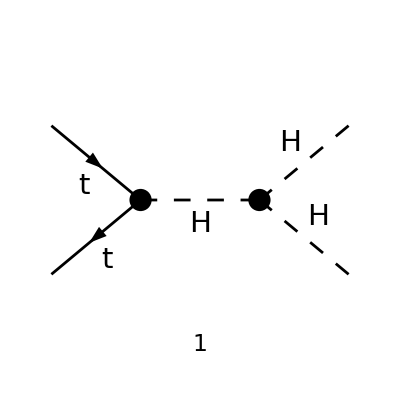

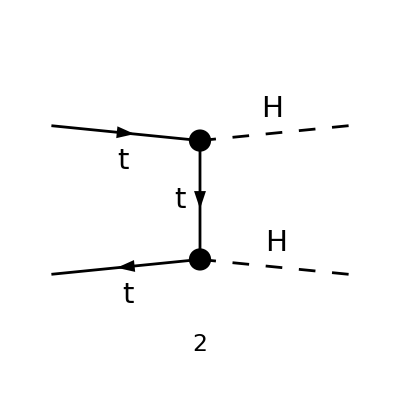

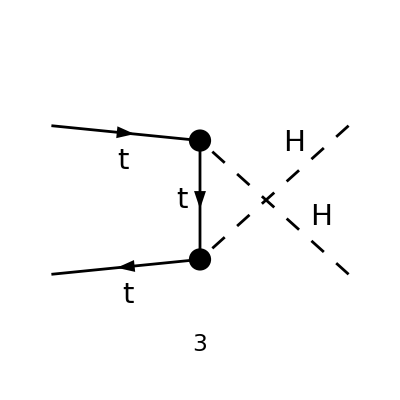

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],-F[3,{3}]}->{S[1],S[1]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1],V[2],V[3],V[1],SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp[0]*ComplexConjugate[amp[0]])]];
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp[0][[i]]*ComplexConjugate[amp[0]][[j]]]]][[1]]];
re[i,j],{i,amp[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.031721

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.033322

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.033953

calculating color factors in products of the    amplitudes 3 and 1 (CC), time = 0.034399

calculating color factors in products of the    amplitudes 3 and 2 (CC), time = 0.03447

calculating color factors in products of the    amplitudes 3 and 3 (CC), time = 0.03391

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.025458,Null}

Doing spin sums2 and 1 (CC), time = {0.034655,Null}

Doing spin sums2 and 2 (CC), time = {0.045887,Null}

Doing spin sums3 and 1 (CC), time = {0.032459,Null}

Doing spin sums3 and 2 (CC), time = {0.046236,Null}

Doing spin sums3 and 3 (CC), time = {0.045005,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.011928

calculating product of the amplitudes 2 and 1 (CC), time = 0.011569

calculating product of the amplitudes 2 and 2 (CC), time = 0.009672

calculating product of the amplitudes 3 and 1 (CC), time = 0.010727

calculating product of the amplitudes 3 and 2 (CC), time = 0.013479

calculating product of the amplitudes 3 and 3 (CC), time = 0.009594

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp[0]//Length},{j,1,amp[0]//Length}]]]
```

(e^4 C_A m_t^2 (m_H^4 (4 s m_t^4 (4 t^2+15 t u+4 u^2)-33 s m_t^8+12 m_t^6 (2 t^2+3 t u+2 u^2)+t u m_t^2 (25 t^2+52 t u+25 u^2)-50 m_t^10+9 s t^2 u^2)-2 s m_H^2 m_t^2 (4 s m_t^2 (t^2+9 t u+u^2)+3 m_t^4 (5 t^2+18 t u+5 u^2)-20 m_t^8+4 t u (t^2+4 t u+u^2))+m_t^2 (s^3 m_t^2 (t^2+12 t u+u^2)+6 s^3 m_t^6+6 s^2 m_t^4 (t^2+6 t u+u^2)-8 s^2 m_t^8+t u (t^2-u^2)^2)))/(2 (t-m_t^2)^2 m_W^4 (s-m_H^2)^2 (u-m_t^2)^2 (sin(θ_W))^4)

```mathematica
ampSquared2=ampSquared[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ϵ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ϵ]&//ReplaceAll[#,SMP["sin_W"]->e/g ϵ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ϵ]&
```

(4 e^4 yt^2 C_A (1/2 v^2 yt^2 ϵ^2 (1/2 s^3 v^2 yt^2 ϵ^2 (t^2+12 t u+u^2)+3/4 s^3 v^6 yt^6 ϵ^6+3/2 s^2 v^4 yt^4 ϵ^4 (t^2+6 t u+u^2)-1/2 s^2 v^8 yt^8 ϵ^8+t u (t^2-u^2)^2)-2 λ s v^4 yt^2 ϵ^4 (2 s v^2 yt^2 ϵ^2 (t^2+9 t u+u^2)+3/4 v^4 yt^4 ϵ^4 (5 t^2+18 t u+5 u^2)+4 t u (t^2+4 t u+u^2)-5/4 v^8 yt^8 ϵ^8)+4 λ^2 v^4 ϵ^4 (s v^4 yt^4 ϵ^4 (4 t^2+15 t u+4 u^2)+9 s t^2 u^2-33/16 s v^8 yt^8 ϵ^8+3/2 v^6 yt^6 ϵ^6 (2 t^2+3 t u+2 u^2)+1/2 t u v^2 yt^2 ϵ^2 (25 t^2+52 t u+25 u^2)-25/16 v^10 yt^10 ϵ^10)))/(e^4 v^2 ϵ^6 (s-2 λ v^2 ϵ^2)^2 (t-1/2 v^2 yt^2 ϵ^2)^2 (u-1/2 v^2 yt^2 ϵ^2)^2)

```mathematica
Series[ampSquared2,{ϵ,0,0}]//Normal//ReplaceAll[#,λ->0]&//Series[#,{v,0,0}]&//Normal//Simplify
```

(2 e^4 yt^4 C_A (t^2-u^2)^2)/(e^4 s^2 t u ϵ^4)

```mathematica
Res=ampSquaredSUNN3[0]//Expand
```

(48 t^3 g_s^4)/(s^2 u)+(48 u^3 g_s^4)/(s^2 t)+(96 t u g_s^4)/s^2-(16 u g_s^4)/(3 t)-(16 t g_s^4)/(3 u)

```mathematica
Res/.u->-s-t//Series[#,{t,0,2}]&
```

-(128 (s g_s^4))/(3 t)-(416 g_s^4)/3-(704 t g_s^4)/(3 s)-(448 t^2 g_s^4)/(3 s^2)+O(t^3)

```mathematica
Litt=8dF*CF^2(u/t+t/u)-8 dF CF CA((t^2+u^2)/s^2)/.RepComp//Expand
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8 dF C_F^2 (t/u+u/t)-(8 dF C_A C_F (t^2+u^2))/s^2/.RepComp

```mathematica
Litt/.u->-s-t//Series[#,{t,0,2}]&
```

ReplaceAll::reps: {RepComp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

8 dF C_F^2 ((-s-t)/t+t/(-s-t))-(8 dF C_A C_F ((-s-t)^2+t^2))/s^2/.RepComp

## q1 h>q1 h

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

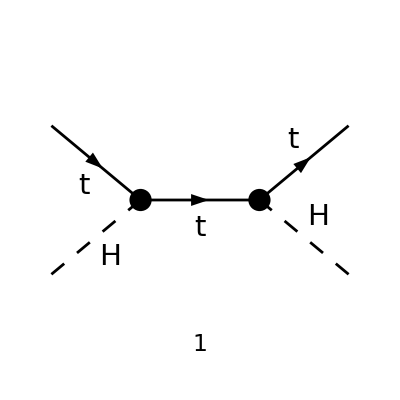

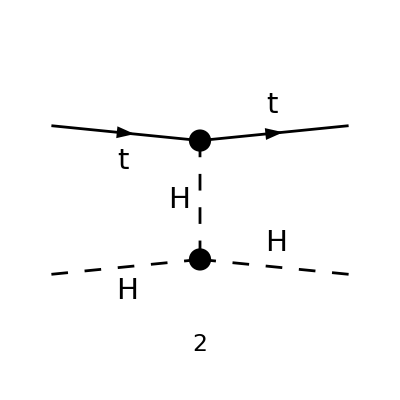

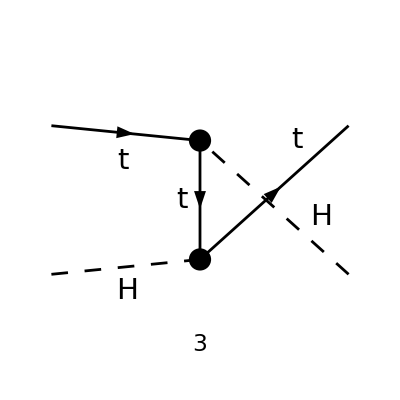

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],S[1]}->{F[3,{3}],S[1]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1],V[2],V[3],V[1],SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&;
```

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

Set::write: Tag Plus in (-(«1»)/((-OverBar[«26»]+OverBar[p2])^2-m_t^2)-(«1»)/((-OverBar[«26»]-OverBar[«26»])^2-m_t^2)-(2 («1») g_s^2 T_Col3Col1^Glu5 (tr(T^Glu2.T^Glu4.T^Glu5)))/(OverBar[«26»]-OverBar[p2])^2)(0) is Protected.

{((φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(γ̄·(OverBar[k_3]+OverBar[k_4])).(-(ⅈ yt)/(√2)).(φ(OverBar[k_1])))/(-OverBar[k_3]-OverBar[k_4])^2,-(6 ⅈ λ v (φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(φ(OverBar[k_1])))/(OverBar[k_4]-OverBar[k_2])^2,((φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(γ̄·(OverBar[k_3]-OverBar[k_2])).(-(ⅈ yt)/(√2)).(φ(OverBar[k_1])))/(OverBar[k_2]-OverBar[k_3])^2}

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.026283

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.000375,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.000688

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

0

```mathematica
AE=Series[ampSquared[0]/.t->-s-u,{u,0,0}]//Normal
```

0

```mathematica
AE=Series[ampSquared[0]/.u->-s-t,{t,0,0}]//Normal
```

0

```mathematica
AE/.t->-s-u//Series[#,{u,0,0}]&
```

0

## q1 h>q1 g

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

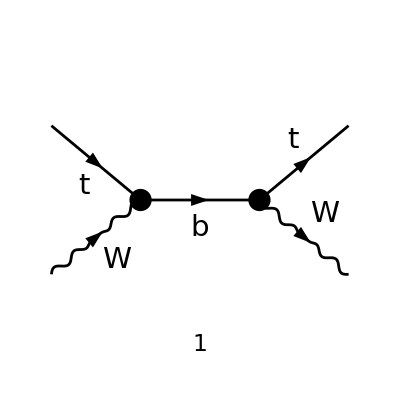

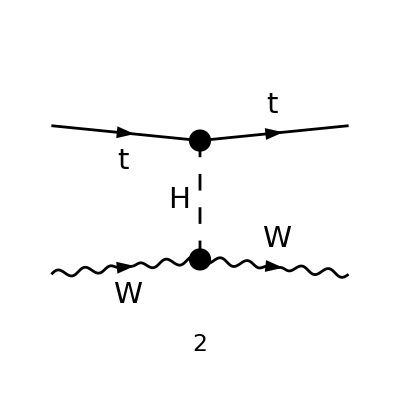

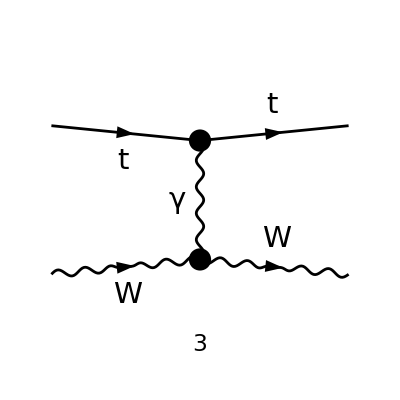

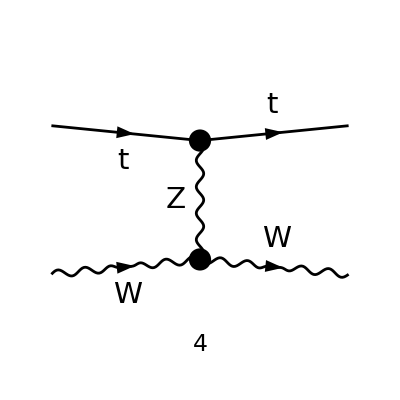

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],V[3]}->{F[3,{3}],V[3]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1],SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True][[2;;2]]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&;
```

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

Set::write: Tag Plus in (-(«1»)/((-OverBar[«26»]+OverBar[p2])^2-m_t^2)-(«1»)/((-OverBar[«26»]-OverBar[«26»])^2-m_t^2)-(2 («1») g_s^2 T_Col3Col1^Glu5 (tr(T^Glu2.T^Glu4.T^Glu5)))/(OverBar[«26»]-OverBar[p2])^2)(0) is Protected.

{(g^2 v yt δ_Col1Col3 (ε̄(k_2)·(ε̄)^*(k_4)) (φ(OverBar[k_3])).(φ(OverBar[k_1])))/(2 √2 (OverBar[k_4]-OverBar[k_2])^2)}

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.02599

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.000389,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k2,k4,1]&)[(polsums[#1,k4,k2,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.000709

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

0

```mathematica
AE=Series[ampSquared[0]/.t->-s-u,{u,0,0}]//Normal
```

0

```mathematica
AE=Series[ampSquared[0]/.u->-s-t,{t,0,0}]//Normal
```

0

```mathematica
AE/.t->-s-u//Series[#,{u,0,0}]&
```

0

## q1 h>q g

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

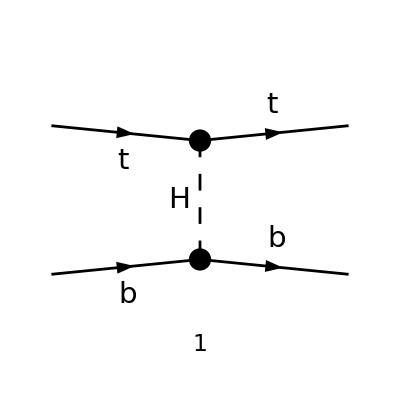

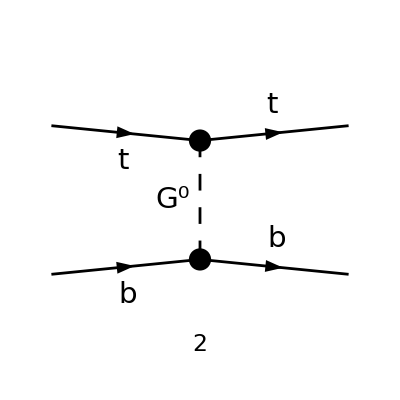

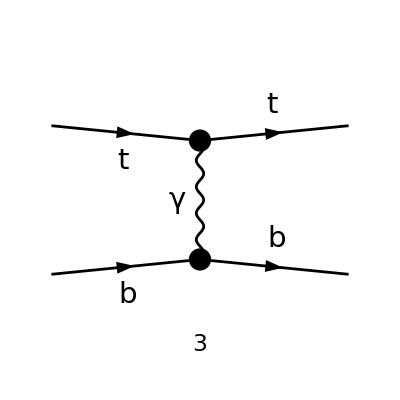

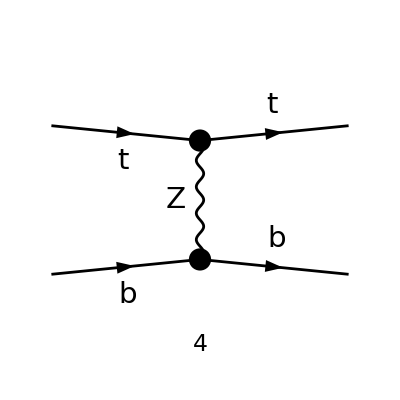

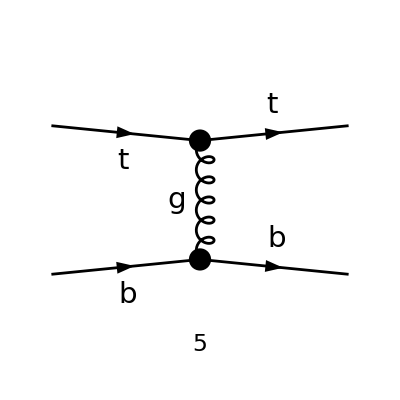

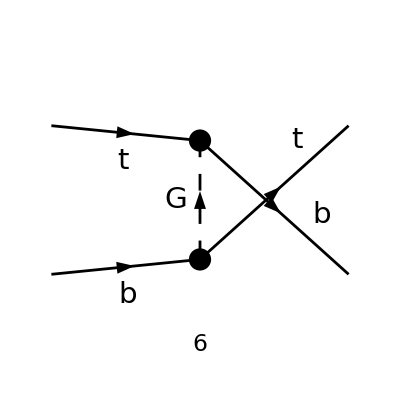

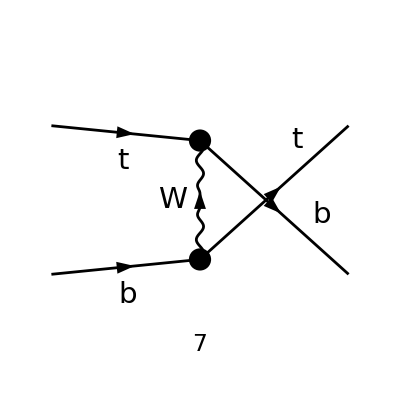

FeynArtsGraphics()(([1]),([2]),([3]),([4]),([5]),([6]),([7]))

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],F[4,{3}]}->{F[3,{3}],F[4,{3}]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1],U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}]
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True][[1;;1]]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&;
```

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

Set::write: Tag Plus in (-(«1»)/((-OverBar[«26»]+OverBar[p2])^2-m_t^2)-(«1»)/((-OverBar[«26»]-OverBar[«26»])^2-m_t^2)-(2 («1») g_s^2 T_Col3Col1^Glu5 (tr(T^Glu2.T^Glu4.T^Glu5)))/(OverBar[«26»]-OverBar[p2])^2)(0) is Protected.

{-((φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(φ(OverBar[k_1])) (φ(OverBar[k_4])).(-(ⅈ m_b δ_Col2Col4)/v).(φ(OverBar[k_2])))/(OverBar[k_4]-OverBar[k_2])^2}

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

ComplexConjugate::warnmsg: Warning! The list of Dirac chains contains Pauli or SU(N) symbols. Their correct complex conjugation is not guaranteed.

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.026117

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.000383,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k2,k4,1]&)[(polsums[#1,k4,k2,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.000712

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

0

```mathematica
AE=Series[ampSquared[0]/.t->-s-u,{u,0,0}]//Normal
```

0

```mathematica
AE=Series[ampSquared[0]/.u->-s-t,{t,0,0}]//Normal
```

0

```mathematica
AE/.t->-s-u//Series[#,{u,0,0}]&
```

0

## t h>t h

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],S[1]}->{F[3,{3}],S[1]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1]SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[amp,amp2]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&//ReplaceAll[#,FCI[Spinor[-Momentum[k3_],x_,1]]:>Spinor[-Momentum[k3],0,1]]&
```

{((φ(OverBar[k_3])).(-(ⅈ e m_t δ_Col1Col3)/(2 m_W (sin(θ_W)))).(γ̄·(OverBar[k_3]+OverBar[k_4])).(-(ⅈ e m_t)/(2 m_W (sin(θ_W)))).(φ(OverBar[k_1])))/(-OverBar[k_3]-OverBar[k_4])^2,-(3 ⅈ e m_H^2 (φ(OverBar[k_3])).(-(ⅈ e m_t δ_Col1Col3)/(2 m_W (sin(θ_W)))).(φ(OverBar[k_1])))/(2 m_W (sin(θ_W)) (OverBar[k_4]-OverBar[k_2])^2),((φ(OverBar[k_3])).(-(ⅈ e m_t δ_Col1Col3)/(2 m_W (sin(θ_W)))).(γ̄·(OverBar[k_3]-OverBar[k_2])).(-(ⅈ e m_t)/(2 m_W (sin(θ_W)))).(φ(OverBar[k_1])))/(OverBar[k_2]-OverBar[k_3])^2}

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

{((φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(γ̄·(OverBar[k_3]+OverBar[k_4])).(-(ⅈ yt)/(√2)).(φ(OverBar[k_1])))/(-OverBar[k_3]-OverBar[k_4])^2,-(6 ⅈ λ v (φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(φ(OverBar[k_1])))/(OverBar[k_4]-OverBar[k_2])^2,((φ(OverBar[k_3])).(-(ⅈ yt δ_Col1Col3)/(√2)).(γ̄·(OverBar[k_3]-OverBar[k_2])).(-(ⅈ yt)/(√2)).(φ(OverBar[k_1])))/(OverBar[k_2]-OverBar[k_3])^2}

```mathematica
Clear[s,t,u]
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.027068

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.027234

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.028056

calculating color factors in products of the    amplitudes 3 and 1 (CC), time = 0.028689

calculating color factors in products of the    amplitudes 3 and 2 (CC), time = 0.029984

calculating color factors in products of the    amplitudes 3 and 3 (CC), time = 0.028439

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.020053,Null}

Doing spin sums2 and 1 (CC), time = {0.014986,Null}

Doing spin sums2 and 2 (CC), time = {0.014057,Null}

Doing spin sums3 and 1 (CC), time = {0.023872,Null}

Doing spin sums3 and 2 (CC), time = {0.016106,Null}

Doing spin sums3 and 3 (CC), time = {0.023717,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.001035

calculating product of the amplitudes 2 and 1 (CC), time = 0.000571

calculating product of the amplitudes 2 and 2 (CC), time = 0.001011

calculating product of the amplitudes 3 and 1 (CC), time = 0.006755

calculating product of the amplitudes 3 and 2 (CC), time = 0.000608

calculating product of the amplitudes 3 and 3 (CC), time = 0.000809

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

-(2 yt^2 C_A (72 λ^2 s u v^2+t^3 yt^2+4 t^2 u yt^2+4 t u^2 yt^2))/(s t u)

```mathematica
ampSquared[0]/.λ->0//FullSimplify
```

-(2 yt^4 C_A (t+2 u)^2)/(s u)

```mathematica
-(2 yt^4 Subscript[C, A] (t+2 u)^2)/(s u)/.t->-u-s//Simplify
```

-(2 yt^4 C_A (s-u)^2)/(s u)

```mathematica
Series[-(2 yt^4 Subscript[C, A] (t+2 u)^2)/(s u)/.t->-u-s,{u,0,0}]//Normal
```

4 yt^4 C_A-(2 s yt^4 C_A)/u

## t h>t g

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

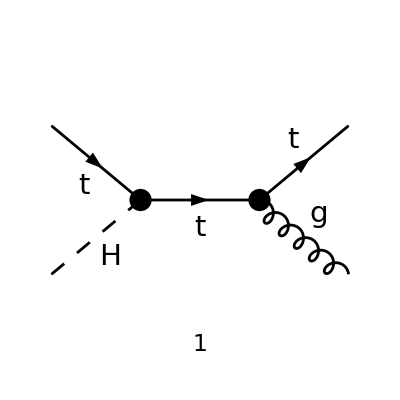

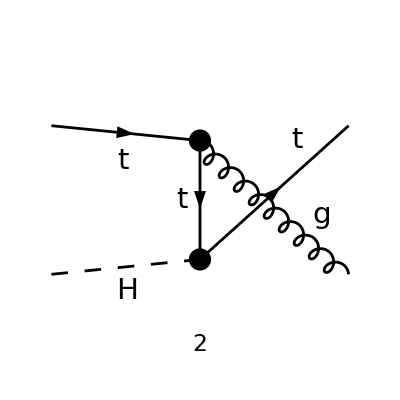

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],S[1]}->{F[3,{3}],V[5]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1]SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp,amp2]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&//ReplaceAll[#,FCI[Spinor[-Momentum[k3_],x_,1]]:>Spinor[-Momentum[k3],0,1]]&
```

{-(e g_s m_t T_Col3Col1^Glu4 (φ(OverBar[k_3])).(γ̄·(ε̄)^*(k_4)).(γ̄·(OverBar[k_3]+OverBar[k_4])).(φ(OverBar[k_1])))/(2 m_W (sin(θ_W)) (-OverBar[k_3]-OverBar[k_4])^2),-(e g_s m_t T_Col3Col1^Glu4 (φ(OverBar[k_3])).(γ̄·(OverBar[k_3]-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(φ(OverBar[k_1])))/(2 m_W (sin(θ_W)) (OverBar[k_2]-OverBar[k_3])^2)}

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

{-(yt g_s T_Col3Col1^Glu4 (φ(OverBar[k_3])).(γ̄·(ε̄)^*(k_4)).(γ̄·(OverBar[k_3]+OverBar[k_4])).(φ(OverBar[k_1])))/(√2 (-OverBar[k_3]-OverBar[k_4])^2),-(yt g_s T_Col3Col1^Glu4 (φ(OverBar[k_3])).(γ̄·(OverBar[k_3]-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(φ(OverBar[k_1])))/(√2 (OverBar[k_2]-OverBar[k_3])^2)}

```mathematica
Clear[s,t,u]
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.021939

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.021753

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.022418

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.045983,Null}

Doing spin sums2 and 1 (CC), time = {0.035197,Null}

Doing spin sums2 and 2 (CC), time = {0.034557,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.015993

calculating product of the amplitudes 2 and 1 (CC), time = 0.025114

calculating product of the amplitudes 2 and 2 (CC), time = 0.015232

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

-(4 t^2 yt^2 C_A C_F g_s^2)/(s u)

```mathematica
ampSquared[0]/.λ->0//FullSimplify
```

-(4 t^2 yt^2 C_A C_F g_s^2)/(s u)

```mathematica
-(4 t^2 yt^2 Subscript[C, A] Subscript[C, F] Subscript[g, s]^2)/(s u)/.t->-u-s//Simplify
```

-(4 yt^2 C_A C_F g_s^2 (s+u)^2)/(s u)

## t t>h g

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

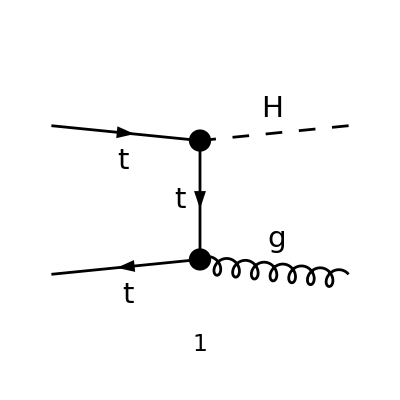

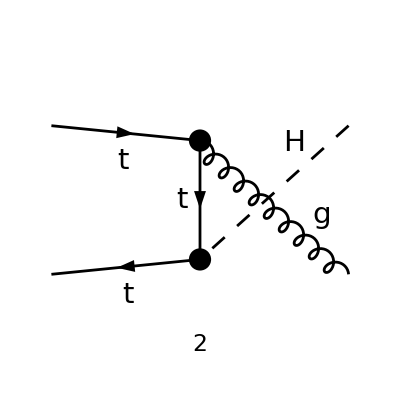

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{3}],-F[3,{3}]}->{S[1],V[5]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{F[1]SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp,amp2]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]//FCI//ReplaceAll[#,FCI[FeynAmpDenominator[PropagatorDenominator[Momentum[p3_],x3_]]]:>FeynAmpDenominator[PropagatorDenominator[Momentum[p3],0]]]&//ReplaceAll[#,FCI[DiracGamma[Momentum[k3_]]+x_]:>DiracGamma[Momentum[k3]]]&//ReplaceAll[#,FCI[Spinor[Momentum[k3_],x_,1]]:>Spinor[Momentum[k3],0,1]]&//ReplaceAll[#,FCI[Spinor[-Momentum[k3_],x_,1]]:>Spinor[-Momentum[k3],0,1]]&
```

{-(e g_s m_t T_Col2Col1^Glu4 (φ(-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(γ̄·(OverBar[k_4]-OverBar[k_2])).(φ(OverBar[k_1])))/(2 m_W (sin(θ_W)) (OverBar[k_2]-OverBar[k_4])^2),-(e g_s m_t T_Col2Col1^Glu4 (φ(-OverBar[k_2])).(γ̄·(OverBar[k_3]-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(φ(OverBar[k_1])))/(2 m_W (sin(θ_W)) (OverBar[k_2]-OverBar[k_3])^2)}

```mathematica
amp2[0]=amp[0]//ReplaceAll[#,SMP["m_W"]->v/2 g ]&//ReplaceAll[#,SMP["m_t"]->v yt/Sqrt[2] ]&//ReplaceAll[#,SMP["sin_W"]->SMP["e"]/g ]&//ReplaceAll[#,SMP["m_H"]->Sqrt[2] v Sqrt[λ] ]&//Simplify
```

{-(yt g_s T_Col2Col1^Glu4 (φ(-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(γ̄·(OverBar[k_4]-OverBar[k_2])).(φ(OverBar[k_1])))/(√2 (OverBar[k_2]-OverBar[k_4])^2),-(yt g_s T_Col2Col1^Glu4 (φ(-OverBar[k_2])).(γ̄·(OverBar[k_3]-OverBar[k_2])).(γ̄·(ε̄)^*(k_4)).(φ(OverBar[k_1])))/(√2 (OverBar[k_2]-OverBar[k_3])^2)}

```mathematica
Clear[s,t,u]
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp2[0]*ComplexConjugate[amp2[0]])]];
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True]&)[FeynAmpDenominatorExplicit[amp2[0][[i]]*ComplexConjugate[amp2[0]][[j]]]]][[1]]];
re[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.021504

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.021678

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.022227

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]];//Simplify]];
re2[i,j],{i,amp2[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.046834,Null}

Doing spin sums2 and 1 (CC), time = {0.037113,Null}

Doing spin sums2 and 2 (CC), time = {0.033352,Null}

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k4,k3,1]&)[(polsums[#1,k3,k4,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp2[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.019248

calculating product of the amplitudes 2 and 1 (CC), time = 0.028683

calculating product of the amplitudes 2 and 2 (CC), time = 0.014217

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp2[0]//Length},{j,1,amp2[0]//Length}]]]
```

(4 s^2 yt^2 C_A C_F g_s^2)/(t u)

```mathematica
ampSquared[0]/.λ->0//FullSimplify
```

(4 s^2 yt^2 C_A C_F g_s^2)/(t u)

```mathematica
-(4 t^2 yt^2 Subscript[C, A] Subscript[C, F] Subscript[g, s]^2)/(s u)/.t->-u-s//Simplify
```

-(4 yt^2 C_A C_F g_s^2 (s+u)^2)/(s u)

# W bosons

## w q1>w q1

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

#### Creating amplitudes

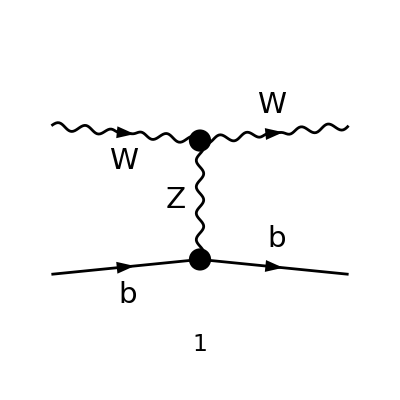

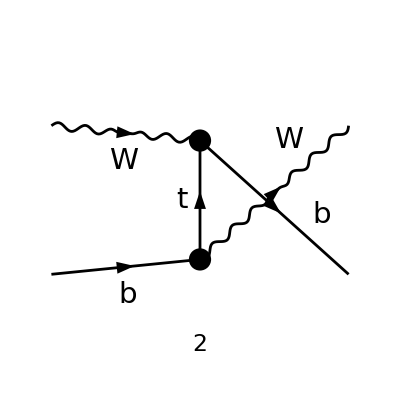

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{V[3],F[4,{3}]}->{V[3],F[4,{3}]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{V[1],S,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp,amp0,amp01,amp02,amp03]
```

```mathematica
amp0[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{V[2],F[4,{3}]}->{V[2],F[4,{3}]},InsertionLevel->{Classes}, Model->"SM",ExcludeParticles->{F[1],V[1],S,U[2],U[3],U[4],U[1]}];
amp01[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
diags=InsertFields[CreateTopologies[0,2->2],{V[2],F[4,{3}]}->{V[3],F[4,{3}]},InsertionLevel->{Classes}, Model->"SM",ExcludeParticles->{F[1],V[1],S,U[2],U[3],U[4],U[1]}];
amp02[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]
diags=InsertFields[CreateTopologies[0,2->2],{V[3],F[4,{3}]}->{V[2],F[4,{3}]},InsertionLevel->{Classes}, Model->"SM",ExcludeParticles->{F[1],V[1],S,U[2],U[3],U[4],U[1]}];
amp03[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True];
```

{}

```mathematica
amp[0]=Join[ amp0[0],  amp01[0],amp02[0],amp03[0]]/.SMP["sin_W"]->SMP["e"]/.SMP["cos_W"]-> 1/.SMP["e"]->0;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
ampSquared[0]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[(amp[1]*ComplexConjugate[amp[0]])]];
```

```mathematica
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]]
```

```mathematica
ClearAll[re];
Table[Print["    calculating color factors in products of the    amplitudes ",i," and ",j," (CC), time = ",Timing[re[i,j]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[amp[0][[i]]*ComplexConjugate[amp[0]][[j]]]]][[1]]];
re[i,j],{i,amp[0]//Length},{j,i}];
```

calculating color factors in products of the    amplitudes 1 and 1 (CC), time = 0.075359

calculating color factors in products of the    amplitudes 2 and 1 (CC), time = 0.056047

calculating color factors in products of the    amplitudes 2 and 2 (CC), time = 0.04764

calculating color factors in products of the    amplitudes 3 and 1 (CC), time = 0.059688

calculating color factors in products of the    amplitudes 3 and 2 (CC), time = 0.051405

calculating color factors in products of the    amplitudes 3 and 3 (CC), time = 0.051089

calculating color factors in products of the    amplitudes 4 and 1 (CC), time = 0.059984

calculating color factors in products of the    amplitudes 4 and 2 (CC), time = 0.051033

calculating color factors in products of the    amplitudes 4 and 3 (CC), time = 0.048759

calculating color factors in products of the    amplitudes 4 and 4 (CC), time = 0.048921

```mathematica
ClearAll[re2];
Table[Print["Doing spin sums",i," and ",j," (CC), time = ",Timing[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]]//ReplaceAll[#,SMP["m_t"]->0]&//ReplaceAll[#,SMP["m_b"]->0]&//ReplaceAll[#,SMP["m_Z"]->0]&;//Simplify]];
re2[i,j],{i,amp[0]//Length},{j,i}];
```

Doing spin sums1 and 1 (CC), time = {0.24038,Null}

Doing spin sums2 and 1 (CC), time = {0.152622,Null}

Doing spin sums2 and 2 (CC), time = {0.159639,Null}

Doing spin sums3 and 1 (CC), time = {0.151672,Null}

Doing spin sums3 and 2 (CC), time = {0.150476,Null}

Doing spin sums3 and 3 (CC), time = {0.141027,Null}

Doing spin sums4 and 1 (CC), time = {0.150521,Null}

Doing spin sums4 and 2 (CC), time = {0.151068,Null}

Doing spin sums4 and 3 (CC), time = {0.153011,Null}

Doing spin sums4 and 4 (CC), time = {0.157701,Null}

```mathematica
ClearAll[pre];
Table[Print["    calculating product of the amplitudes ",i," and ",j," (CC), time = ",Timing[pre[i,j]=Simplify[(polsums[#1,k1,k3,1]&)[(polsums[#1,k3,k1,1]&)[re2[i,j]]]]][[1]]];
pre[i,j],{i,amp[0]//Length},{j,i}];
```

calculating product of the amplitudes 1 and 1 (CC), time = 0.237974

calculating product of the amplitudes 2 and 1 (CC), time = 0.345241

calculating product of the amplitudes 2 and 2 (CC), time = 0.264982

calculating product of the amplitudes 3 and 1 (CC), time = 0.340269

calculating product of the amplitudes 3 and 2 (CC), time = 0.289789

calculating product of the amplitudes 3 and 3 (CC), time = 0.21143

calculating product of the amplitudes 4 and 1 (CC), time = 0.341161

calculating product of the amplitudes 4 and 2 (CC), time = 0.268189

calculating product of the amplitudes 4 and 3 (CC), time = 0.350548

calculating product of the amplitudes 4 and 4 (CC), time = 0.272129

```mathematica
fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp[0]//Length},{j,1,amp[0]//Length}]]]
```

-(N (s^2+u^2) (t v2-2 s v1)^2)/(4 s t^2 u)

```mathematica
ampFinal2=ampSquared[0]/.SMP["sin_W"]->SMP["e"]/.SMP["cos_W"]-> 1/.SMP["e"]->0//Expand//ReplaceAll[#,v1 v2->0]&//FullSimplify//Expand
```

-(N s^3 v1^2)/(t^2 u)-(N s u v1^2)/t^2-(N s v2^2)/(4 u)-(N u v2^2)/(4 s)

# Automatized

```mathematica
CalculateAmplitude[Vec1_,Vec2_,Fer1_,Fer2_]:=Module[{},
diags=InsertFields[CreateTopologies[0,2->2],{Vec1,Vec2}->{Fer1,Fer2},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{V[1],U[2],U[3],U[4],U[1]}];
Clear[amp];
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]/.SMP["sin_W"]->SMP["e"]/.SMP["cos_W"]-> 1//ReplaceAll[#,SMP["m_t"]->0]&//ReplaceAll[#,SMP["m_b"]->0]&//ReplaceAll[#,SMP["m_Z"]->0]&//ReplaceAll[#,SMP["m_W"]->0]&//ReplaceAll[#,SMP["m_H"]->0]&;
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
polsums[x_,vec_,aux_,spinfac_]:=(FixedPoint[ReleaseHold,#1]&)[(DoPolarizationSums[#1,vec,aux,ExtraFactor->spinfac]&)[(Isolate[#1,{Polarization[vec,__]}]&)[(Collect2[#1,Pair[_,Momentum[Polarization[vec,__]]]]&)[x]]]];
ClearAll[re];
Table[re[i,j]=(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[amp[0][[i]]*ComplexConjugate[amp[0]][[j]]]],{i,amp[0]//Length},{j,i}];
ClearAll[re2];
Table[re2[i,j]=DiracSimplify[(FermionSpinSum[#1]&)[re[i,j]]]//ReplaceAll[#,SMP["m_t"]->0]&//ReplaceAll[#,SMP["m_b"]->0]&//Simplify;,{i,amp[0]//Length},{j,i}];
ClearAll[pre];
Table[pre[i,j]=Simplify[(polsums[#1,k2,k1,1]&)[(polsums[#1,k3,k2,1]&)[(polsums[#1,k1,k3,1]&)[(polsums[#1,k4,k2,1]&)[re2[i,j]]]]]],{i,amp[0]//Length},{j,i}];

fpre[i_,j_]:=pre[i,j]/;i>=j;
fpre[i_,j_]:=ComplexConjugate[pre[j,i]]/;i<j;
ampSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[Sum[fpre[i,j],{i,1,amp[0]//Length},{j,1,amp[0]//Length}]]];

ampFinal2=ampSquared[0]/.SMP["sin_W"]->SMP["e"]/.SMP["cos_W"]-> 1//Expand//FullSimplify//Expand//ReplaceAll[#,SMP["m_Z"]->0]&//ReplaceAll[#,SMP["m_W"]->0]&//ReplaceAll[#,SMP["m_H"]->0]&//ReplaceAll[#,SMP["e"]->0]&;
Return[ampFinal2]
];
```

## w w>w w

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

```mathematica
Vec1={V[2],V[3],-V[3]};
```

```mathematica
Vec2={V[2],V[3],-V[3]};
```

```mathematica
S1={S[1],S[2],S[3],-S[3]};
```

```mathematica
ClearAll[CrossSec];
```

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{Vec1[[2]],Vec1[[3]]}->{Vec1[[2]],Vec1[[3]]},InsertionLevel->{Classes}, Model->"SMQCD",ExcludeParticles->{V[1],S,U[2],U[3],U[4],U[1]}];
```

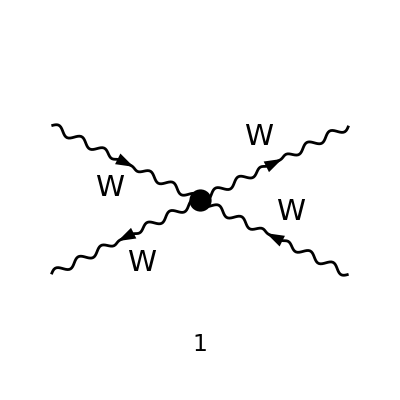

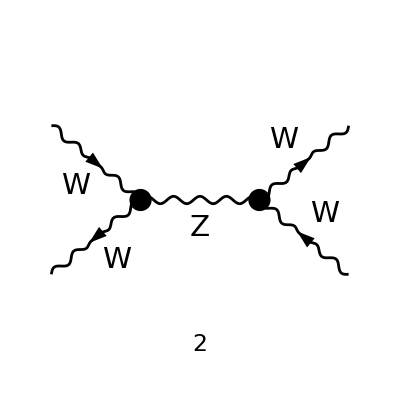

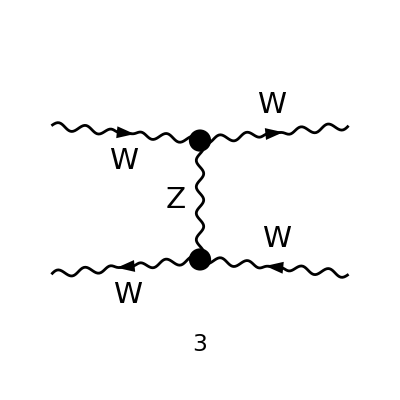

```mathematica
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
CrossSec=Sum[
CalculateAmplitude[Vec1[[a]],Vec1[[i]],Vec1[[b]],Vec1[[j]]],{a,1,3},{b,1,3},{i,1,3},{j,1,3}
];
```

```mathematica
CrossSec
```

(96 t^4)/(s^2 u^2)+(192 t^3)/(s^2 u)+(96 u^4)/(s^2 t^2)+(384 t^2)/s^2+(192 u^3)/(s^2 t)+(384 t u)/s^2+(384 u^2)/s^2+(96 t^2)/u^2+(96 u^2)/t^2+(192 t)/u+(192 u)/t+288

```mathematica
Litt=3-s u/t^2-s t /u^2- t u /s^2;
```

## w s>w s

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

```mathematica
Vec1={V[2],V[3],-V[3]};
```

```mathematica
Vec2={V[2],V[3],-V[3]};
```

```mathematica
S1={S[1],S[2],S[3],-S[3]};
```

```mathematica
ClearAll[CrossSec];
```

```mathematica
CrossSec=Sum[
CalculateAmplitude[Vec1[[a]],S1[[i]],Vec2[[b]],S1[[j]]],{a,1,3},{b,1,3},{i,1,4},{j,1,4}
];
```

## w w>ss

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

### The calculation

```mathematica
Vec1={V[2],V[3],-V[3]};
```

```mathematica
Vec2={V[2],V[3],-V[3]};
```

```mathematica
S1={S[1],S[2],S[3],-S[3]};
```

```mathematica
ClearAll[CrossSec];
```

```mathematica
CrossSec=Sum[
CalculateAmplitude[Vec1[[a]],Vec2[[b]],S1[[i]],S1[[j]]],{a,1,3},{b,1,3},{i,1,4},{j,1,4}
];
```

```mathematica
CrossSec
```

(56 t^2)/s^2-(80 t u)/s^2+(56 u^2)/s^2+16

-((s N u (4 v1^2 (2 t^2 m_t^4-4 t u m_Z^2 m_t^2+(s^2+3 u^2) m_Z^4-2 t (s^2+u^2) m_Z^2+t^2 (s^2+u^2)) m_b^8+8 v1 (t (t (2 t v1+t v2+2 u v2)-(t+2 u) v2 m_Z^2) m_t^4+((t^2+3 u t+4 u^2) v2 m_Z^4-2 t (2 t u v1+(s^2+u^2) v2) m_Z^2-s t^3 v2) m_t^2+(s^2 t v1-u (v2 t^2+3 u (v2-v1) t+4 u^2 v2)) m_Z^4+t (u (2 v2 t^2-2 u v1 t+5 u v2 t+6 u^2 v2)-2 s^2 t v1) m_Z^2+t^2 (s^2+u^2) (t v1-u v2)) m_b^6+2 (((3 t^2+8 u t+8 u^2) v2^2 m_Z^4-2 t v2 ((2 v1+3 v2) t^2+4 u (v1+2 v2) t+8 u^2 v2) m_Z^2+t^2 ((4 v1^2+4 v2 v1+3 v2^2) t^2+8 u (-v1^2+v2 v1+v2^2) t+8 u^2 (v2^2-v1^2))) m_t^4+2 (v2 (3 v1 t^3+u (8 v1-3 v2) t^2+2 u^2 (5 v1-4 v2) t-8 u^3 v2) m_Z^4+2 t (4 (v1^2+2 v2^2) u^3+t (4 v1^2-3 v2 v1+8 v2^2) u^2+t^2 (3 v2^2-2 v1^2) u-3 s^2 t v1 v2) m_Z^2+t^2 v2 (v1 t^3-3 u v2 t^2+2 s^2 v1 t-8 u^2 v2 t-8 u^3 v2)) m_t^2+(2 s^2 (t^2-2 u t-2 u^2) v1^2+u (-6 v1 v2 t^3+u (6 v1^2-16 v2 v1+3 v2^2) t^2-4 u^2 (3 v1^2+5 v2 v1-2 v2^2) t+4 u^3 (2 v2^2-3 v1^2))) m_Z^4+2 t (u (6 v1 v2 t^3+u (-2 v1^2+14 v2 v1-3 v2^2) t^2+4 u^2 (v1^2+4 v2 v1-2 v2^2) t+4 u^3 (v1^2-2 v2^2))-2 s^2 (t^2-2 u t-2 u^2) v1^2) m_Z^2+t^2 (2 v1 (v1 t^2-u (2 v1+3 v2) t-2 u^2 v1) s^2+u^2 ((2 v1^2+3 v2^2) t^2-2 u (2 v1^2+3 v2 v1-4 v2^2) t-4 u^2 (v1^2-2 v2^2)))) m_b^4+4 (t ((s^2+u^2) v2^2 m_Z^4-2 v2 (t v2 s^2+u (t+2 u) v1 s+t u^2 v2) m_Z^2+t (t u^2 v2^2+s^2 t v2^2+2 s u v1 (2 t v1+t v2+2 u v2))) m_t^4+(-v2 (-v1 t^4+6 u^2 v1 t^2+2 ((7 v1+v2) u^3+s^2 v2 u) t+8 u^4 v1) m_Z^4+2 t (v2 (-v1 t^2+2 u (v1+v2) t+2 u^2 v1) s^2-4 t u^2 v1^2 s+u^2 v2 (-v1 t^2+2 u (v1+v2) t+2 u^2 v1)) m_Z^2+t^3 v2 (v1 t^3-2 u^2 v1 t-2 ((v1+v2) u^3+s^2 v2 u))) m_t^2+u ((2 t v1^2 s^3+t u v2^2 s^2+6 t u^2 v1^2 s+v2 (-v1 t^4+6 u^2 v1 t^2+u^3 (14 v1+v2) t+8 u^4 v1)) m_Z^4-2 t (2 t v1^2 s^3+t u v2^2 s^2+2 t u^2 v1^2 s+v2 (-v1 t^4+5 u^2 v1 t^2+u^3 (11 v1+v2) t+6 u^4 v1)) m_Z^2+t^2 (s^2+u^2) (2 s t v1^2+v2 (-v1 t^2+u (2 v1+v2) t+2 u^2 v1)))) m_b^2+t^2 m_t^4 ((s^2+u^2) v2^2 m_Z^4-2 t (s^2+u^2) v2^2 m_Z^2+t^2 u^2 v2^2+s^2 (8 u^2 v1^2+t^2 v2^2))-2 t u m_t^2 (-((s^2+u^2) v2 (2 s v1-t v2) m_Z^4)+(4 t v1 v2 s^3+(8 u^2 v1^2-2 t^2 v2^2) s^2+4 t u^2 v1 v2 s-2 t^2 u^2 v2^2) m_Z^2+t^2 (s^2+u^2) v2 (t v2-2 s v1))+u^2 ((4 v1^2 s^4-4 t v1 v2 s^3+(12 u^2 v1^2+t^2 v2^2) s^2-4 t u^2 v1 v2 s+t^2 u^2 v2^2) m_Z^4-2 t (s^2+u^2) (t v2-2 s v1)^2 m_Z^2+t^2 (s^2+u^2) (t v2-2 s v1)^2)))/(4 t^2 (s-m_b^2)^2 (u-m_b^2)^2 (u-m_t^2)^2 (t-m_Z^2)^2))